FittedModel[0.486564-5.0774×10^-7 x^2]

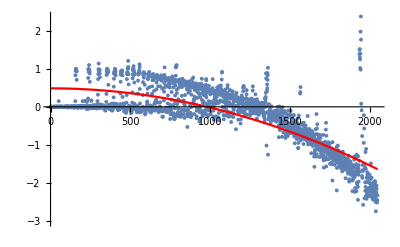

0.635516

{1.72316×10^-153,1.15320983513×10^-418}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "as-fixed"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a +c*x^2,{a,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```